## Cálculo de las secciones transversales empleando el modelo Drude-Lorentz

En este Notebook se emplean las definiciones del modelo de Drude-Lorentz de Rakic en https://doi.org/10.1364/ao.37.005271
- Para el modelo de Drude se emplea
ϵ_Drude=1-(f_0 ω_p^2)/(ω (ω - i γ_0))
- Para el modelo de Lorentz se emplea
ϵ_Lorentz=∑_(j=1)^k 1+(f_j ω_p^2)/(ω_j^2-ω^2-iγω)
de tal forma que se obtiene

```mathematica
h=4.135667696*10^(-15); (*eV s*)
hbar=6.582119569*10^(-16); (*eV s*)
vlight=3*^17 ;(*nm s^-1*)
omega=Range[1,10,0.01];
vFAu=1.40*10^(15);(*nm/s*)
vFAg=1.39*10^(15);(*nm/s*)
hvFAu=(1.40*10^(15))*hbar;(*nm/s*)
hvFAg=1.39*10^(15)*hbar;(*nm/s*)
```

```mathematica
hvFAu
```

0.921497

```mathematica
fjAu1=List[0.760,0.024,0.010,0.071,0.601,4.384];
gammaAu1=List[0.053,0.241,0.345,0.870,2.494,2.214];
omegaAu1=List[0,0.415,0.830,2.969,4.304,13.32];
omegaPAu1=9.03;
```

```mathematica
fjAu=List[0.98,0.1222,0.2492,2.7845,0.1082,7.8214];
gammaAu=List[0.04411,0.97329,1.1139,0.4637,0.70308,0.4897];
omegaAu=List[0,3.5684,4.2132,9.1499,2.9144,38.9633];
omegaPAu=8.45;
```

```mathematica
ϵDrude[ω_,ωp_,gamma_,fj_]:=1-((fj[[1]]*ωp^2)/((ω)(ω+I * gamma[[1]])));(*recibe en eV*)
ϵDrudeSC[ω_,ωp_,gamma_,fj_,hvF_,a_,b_,c_]:=1-((fj[[1]]*ωp^2)/((ω)(ω+I *(gamma[[1]]+(hvF/(a b c)^(1/3))))));
ϵLorentz[ω_,ωp_,j_,fj_,omega_,gamma_]:=Sum[((fj[[i]]*(ωp)^2)/(((omega[[i]])^2-(ω)^2)-I * (ω)(gamma[[i]]))),{i,2,j}];
ϵ0Tot[ω_,ωp_,j_,fj_,omega_,gamma_]:=ϵDrude[ω,ωp,gamma,fj]+ϵLorentz[ω,ωp,j,fj,omega,gamma];(*recibe en eV*)
ϵ0TotSC[ω_,ωp_,j_,fj_,omega_,gamma_,vF_,a_,b_,c_]:=ϵDrudeSC[ω,ωp,gamma,fj,vF,a,b,c]+ϵLorentz[ω,ωp,j,fj,omega,gamma];
```

```mathematica
ϵDrudeSC[1,9.03,gammaAu,fjAu,hbar*vFAu,5,5,5]
ϵDrudeSC[2,9.03,gammaAu,fjAu,hbar*vFAu,20,20,10]
ϵDrudeSC[3,9.03,gammaAu,fjAu,hbar*vFAu,20,20,10]
```

-74.9478+17.3472 ⅈ

-18.9255+1.0178 ⅈ

-7.86861+0.302008 ⅈ

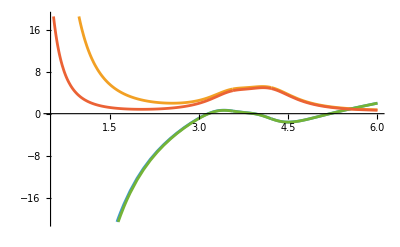

```mathematica
Plot[{Re[ϵ0TotSC[ℏω,omegaPAu,4,fjAu,omegaAu,gammaAu,hbar*vFAu,5,5,3]],Im[ϵ0TotSC[ℏω,omegaPAu,4,fjAu,omegaAu,gammaAu,hbar*vFAu,5,5,3]],Re[ϵ0Tot[ℏω,omegaPAu,4,fjAu,omegaAu,gammaAu]],Im[ϵ0Tot[ℏω,omegaPAu,4,fjAu,omegaAu,gammaAu]]},{ℏω,0.5,6}]
```

```mathematica
au=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Congreso-2025\\Programas\\Olmon-sc.csv"];
nau1=Drop[Drop[au,{450,899}],1];
kau1=Drop[au,{1,451}];
nau1num=Map[ToExpression,nau1,{2}];
kau1num=Map[ToExpression,kau1,{2}];
λAu=nau1num[[All,1]]*1000; (*λ en um*)
ℏωAu=h vlight/λAu; (*eV*)
nau=nau1num[[All,2]];
kAu=kau1num[[All,2]];
nAu=nau+ I kAu;
```

```mathematica
epsReal=Re[nAu^2];
epsImag=Im[nAu^2];
```

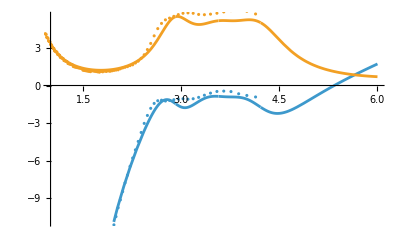

```mathematica
auReal = Transpose[{ℏωAu,epsReal}];
auImag = Transpose[{ℏωAu,epsImag}];
Show[Plot[{Style[Re[ϵ0Tot[x,omegaPAu,5,fjAu,omegaAu,gammaAu]]],Style[Im[ϵ0Tot[x,omegaPAu,5,fjAu,omegaAu,gammaAu]]]},{x,1,6}],ListPlot[{auReal,auImag}]]
```

```mathematica
elipsoblato[a_,b_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1,L2,L3},
							L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L2=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L3=1-2 L1;
{L1,L2,L3}]
```

```mathematica
elipsprolato[a_,b_,c_]:=Module[{eab2=1-(b^2/a^2),L1,L2,L3},
							L1=((1-eab2)/eab2) (-1+((1/(2*Sqrt[eab2]))* Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])]));
							L2=0.5*(1-L1);
							L3=0.5*(1-L1);{L1,L2,L3}];
```

```mathematica
factgeom[j_,a_,b_,c_]:=Which[a==b==c,1/3,a==b ,elipsoblato[a,b,c][[j]],
							b==c ,elipsprolato[a,b,c][[j]]]
```

```mathematica
Cabs[a_,b_,c_,nm_,w_,wp_,j_,fj_,omega0_,gamma_]:=Module[{ϵDrude,ϵLorentz,ϵTot,ϵm,k,αx,αz,CabsTot,αxLorentz,αzLorentz,CabsLorentz},
										ϵm=nm^2;
										k=(2 Pi nm w/(h vlight));
										ϵDrude=1-((fj[[1]]*wp^2)/((w)(w+I * gamma[[1]])));
										ϵLorentz=Sum[((fj[[i]]*(wp)^2)/(((omega0[[i]])^2-(w)^2)-I * (w)(gamma[[i]]))),{i,2,j}];
										ϵTot=ϵDrude+ϵLorentz;
										αx=4 π a b^2  ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵTot-ϵm)));
										αz=4 π a b^2 ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵTot-ϵm)));
										αxLorentz=4 π a b^2  ((ϵLorentz-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵLorentz-ϵm)));
										αzLorentz=4 π a b^2 ((ϵLorentz-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵLorentz-ϵm)));
										CabsTot=k Im[2 αx+αz]/3;
										CabsLorentz=k Im[2 αxLorentz+αzLorentz]/3;{CabsTot,CabsLorentz}]
```

```mathematica
Csca[a_,b_,c_,nm_,w_,wp_,j_,fj_,omega_,gamma_]:=Module[{ϵDrude,ϵLorentz,ϵTot,ϵm,k,αx,αz,CscaTot,αxLorentz,αzLorentz,CscaLorentz},
										ϵm=nm^2;
										k=(2 Pi nm w/(h vlight));
										ϵDrude=1-((fj[[1]]*wp^2)/((w)(w+I * gamma[[1]])));
										ϵLorentz=Sum[((fj[[i]]*(wp)^2)/(((omega[[i]])^2-(w)^2)-I * (w)(gamma[[i]]))),{i,2,j}];
										ϵTot=ϵDrude+ϵLorentz;
										αx=4 π a b^2  ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵTot-ϵm)));
										αz=4 π a b^2 ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵTot-ϵm)));
										αxLorentz=4 π a b^2  ((ϵLorentz-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵLorentz-ϵm)));
										αzLorentz=4 π a b^2 ((ϵLorentz-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵLorentz-ϵm)));
										CscaTot=k^4 Norm[2 αx+αz]^2/(18 Pi);
										CscaLorentz=k^4 Norm[2 αxLorentz+αzLorentz]^2/(18 Pi);{CscaTot,CscaLorentz}]
Cext[a_,b_,c_,nm_,w_,wp_,j_,fj_,omega_,gamma_]:=Csca[a,b,c,nm,w,wp,j,fj,omega,gamma]+Cabs[a,b,c,nm,w,wp,j,fj,omega,gamma];
```

```mathematica
h vlight/1937
```

0.640527

```mathematica
qextAu0=Table[{w,Cext[2.25,2.25,1.0,1.33,w,9.083,1,fjAu,omegaAu,gammaAu][[1]]},{w,0.5,10,0.01}];
qextAu1=Table[{w,Cext[2.25,2.25,2.25,1.33,w,9.083,1,fjAu,omegaAu,gammaAu][[1]]},{w,0.5,10,0.01}];
qextAu2=Table[{w,Cext[1.5,1.5,1.0,1.33,w,9.083,2,fjAu,omegaAu,gammaAu][[2]]},{w,0.5,6,0.01}];
qextAu3=Table[{w,Cext[1.5,1.5,1.0,1.33,w,9.083,5,fjAu,omegaAu,gammaAu][[1]]},{w,0.5,6,0.01}];
```

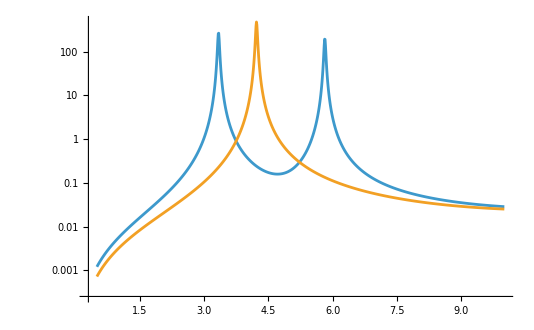

```mathematica
ListLinePlot[{qextAu0,qextAu1},PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
fjAg=List[0.845,0.065,0.124,0.011,0.840,5.646];
gammaAg=List[0.048,3.886,0.452,0.065,0.916,2.419];
omegaAg=List[0,0.816,4.481,8.185,9.083,20.29];
omegaPAg=9.01;
```

```mathematica
ag=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Congreso-2025\\Programas\\Johnson Plata.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en um*)
ℏωAg=h vlight/λAg; (*eV*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
epsRealAg=Re[nAgg^2]
epsImagAg=Im[nAgg^2]
agReal = Transpose[{ℏωAg,epsRealAg}];
agImag = Transpose[{ℏωAg,epsImagAg}];
```

{-0.324044,-0.307824,-0.320625,-0.331129,-0.357116,-0.328944,-0.315625,-0.296496,-0.238464,-0.218736,-0.203049,-0.230289,-0.208884,-0.213221,-0.171549,-0.101269,0.022016,0.216539,0.390404,0.584179,0.866304,0.897444,0.502436,-0.658341,-1.28456,-2.00356,-2.74075,-3.472,-4.2824,-5.17312,-6.05984,-7.05805,-8.22866,-9.56415,-11.0465,-12.8558,-14.8817,-17.2355,-20.0948,-23.4046,-27.4777,-32.7969,-39.8397,-48.8865,-60.7604,-77.9255,-101.993,-140.4,-198.189}

```mathematica
ℏωAg
```

{6.60298,6.47547,6.35279,6.22529,6.10281,5.98505,5.85512,5.73337,5.60389,5.48497,5.36403,5.23281,5.11418,4.98273,4.86358,4.74274,4.61398,4.49366,4.36252,4.24316,4.1233,3.99324,3.87235,3.74269,3.62248,3.50282,3.37238,3.25216,3.12204,3.00194,2.882,2.75161,2.63195,2.50192,2.38184,2.26158,2.13142,2.01151,1.88127,1.76111,1.64114,1.51102,1.39092,1.26087,1.14035,1.02031,0.890668,0.770621,0.640527}

```mathematica
h vlight/50
```

24.814

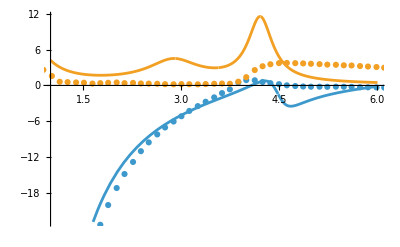

```mathematica
Show[Plot[{Style[Re[ϵ0Tot[x,omegaPAg,5,fjAg,omegaAg,gammaAg]]],Style[Im[ϵ0Tot[x,omegaPAg,5,fjAu,omegaAu,gammaAg]]]},{x,1,6}],ListPlot[{agReal,agImag}]]
```

```mathematica
agReal = Interpolation[Transpose[{hbarraomegaAg,epsRealAg}]];
agImag = Interpolation[Transpose[{hbarraomegaAg,epsImagAg}]];
```

```mathematica
qextAg0=Table[{λ,Cext[1.5,1.5,1.0,1.33,λ,10,1,fjAg,omegaAg,gammaAg][[1]]},{λ,1,10,0.01}];
qextAg1=Table[{λ,Cext[1.5,1.5,1.0,1.33,λ,10,2,fjAg,omegaAg,gammaAg][[1]]},{λ,1,10,0.01}];
qextAg2=Table[{λ,Cext[1.5,1.5,1.0,1.33,λ,10,3,fjAg,omegaAg,gammaAg][[1]]},{λ,1,10,0.01}];
qextAg3=Table[{λ,Cext[1.5,1.5,1.0,1.33,λ,10,4,fjAg,omegaAg,gammaAg][[1]]},{λ,1,10,0.01}];
qextAg4=Table[{λ,Cext[1.5,1.5,1.0,1.33,λ,10,5,fjAg,omegaAg,gammaAg][[1]]},{λ,1,10,0.01}];
qextAg5=Table[{λ,Cext[1.5,1.5,1.0,1.33,λ,10,6,fjAg,omegaAg,gammaAg][[1]]},{λ,1,10,0.01}];
```

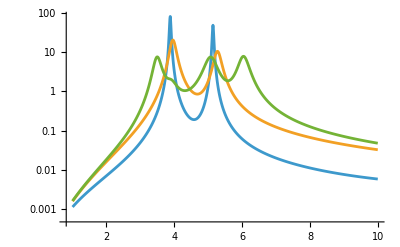

```mathematica
ListLinePlot[{qextAg0,qextAg1,qextAg2},PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
Cext[1.5,1.5,1.0,1.33,1,10,2,fjBi,omegaBi,gammaBi][[1]]
Cext[1.5,1.5,1.0,1.33,1,10,3,fjBi,omegaBi,gammaBi][[2]]
```

0.00216287

0.00202591

```mathematica
CabsSC[a_,b_,c_,nm_,w_,wp_,j_,fj_,omega0_,gamma_,hvF_]:=Module[{ϵDrude,ϵLorentz,ϵTot,ϵm,k,gammaSC,αx,αz,CabsTot,αxLorentz,αzLorentz,CabsLorentz},
										ϵm=nm^2;
										k=(2 Pi nm w/(h vlight));
										gammaSC=gamma[[1]]+(hvF/(a b c)^(-1/3));
										ϵDrude=1-((fj[[1]]*wp^2)/((w)(w+I *gammaSC)));
										ϵLorentz=Sum[((fj[[i]]*(wp)^2)/(((omega0[[i]])^2-(w)^2)-I * (w)(gamma[[i]]))),{i,2,j}];
										ϵTot=ϵDrude+ϵLorentz;
										αx=4 π a b^2  ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵTot-ϵm)));
										αz=4 π a b^2 ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵTot-ϵm)));
										αxLorentz=4 π a b^2  ((ϵLorentz-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵLorentz-ϵm)));
										αzLorentz=4 π a b^2 ((ϵLorentz-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵLorentz-ϵm)));
										CabsTot=k Im[2 αx+αz]/3;
										CabsLorentz=k Im[2 αxLorentz+αzLorentz]/3;{CabsTot,CabsLorentz}]
```

```mathematica
CscaSC[a_,b_,c_,nm_,w_,wp_,j_,fj_,omega_,gamma_,hvF_]:=Module[{ϵDrude,ϵLorentz,ϵTot,ϵm,k,gammaSC,αx,αz,CscaTot,αxLorentz,αzLorentz,CscaLorentz},
										ϵm=nm^2;
										k=(2 Pi nm w/(h vlight));
										gammaSC=gamma[[1]]+(hvF/(a b c)^(-1/3));
										ϵDrude=1-((fj[[1]]*wp^2)/((w)(w+I *gammaSC)));
										ϵLorentz=Sum[((fj[[i]]*(wp)^2)/(((omega[[i]])^2-(w)^2)-I * (w)(gamma[[i]]))),{i,2,j}];
										ϵTot=ϵDrude+ϵLorentz;
										αx=4 π a b^2  ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵTot-ϵm)));
										αz=4 π a b^2 ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵTot-ϵm)));
										αxLorentz=4 π a b^2  ((ϵLorentz-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵLorentz-ϵm)));
										αzLorentz=4 π a b^2 ((ϵLorentz-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵLorentz-ϵm)));
										CscaTot=k^4 Norm[2 αx+αz]^2/(18 Pi);
										CscaLorentz=k^4 Norm[2 αxLorentz+αzLorentz]^2/(18 Pi);{CscaTot,CscaLorentz}]
CextSC[a_,b_,c_,nm_,w_,wp_,j_,fj_,omega_,gamma_,vF_]:=CscaSC[a,b,c,nm,w,wp,j,fj,omega,gamma,vF]+CabsSC[a,b,c,nm,w,wp,j,fj,omega,gamma,vF];
```

```mathematica
h vlight/4.22
```

294.005

```mathematica
qextAu0=Table[{w,Cext[1.5,1.5,1.0,1.33,w,9.083,1,fjAu,omegaAu,gammaAu][[1]]},{w,1,7,0.01}];
qextAu1=Table[{w,Cext[1.5,1.5,1.5,1.33,w,9.083,1,fjAu,omegaAu,gammaAu][[1]]},{w,1,7,0.01}];
```

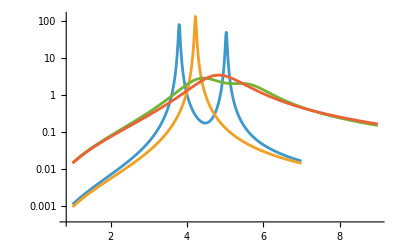

```mathematica
ListLinePlot[{qextAu0,qextAu1,qextAu0SC,qextAu1SC},PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
qextAu0SC=Table[{w,CextSC[1.5,1.5,1.0,1,w,omegaPAu,2,fjAu,omegaAu,gammaAu,hvFAu][[1]]},{w,1,7,0.01}];
qextAu1SC=Table[{w,CextSC[1.5,1.5,1.5,1,w,omegaPAu,2,fjAu,omegaAu,gammaAu,hvFAu][[1]]},{w,1,7,0.01}];
```

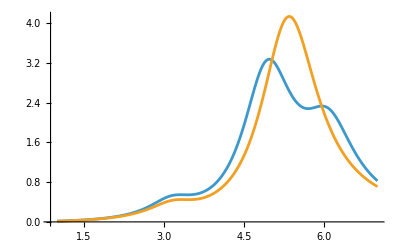

```mathematica
ListLinePlot[{qextAu0SC,qextAu1SC},PlotRange->All]
```

```mathematica
qextAg0=Table[{w,Cext[1.5,1.5,1.0,1,w,omegaPAg,1,fjAg,omegaAg,gammaAg][[1]]},{w,1,7,0.01}];
qextAg1=Table[{w,Cext[1.5,1.5,1.5,1,w,omegaPAg,1,fjAg,omegaAg,gammaAg][[1]]},{w,1,7,0.01}];
```

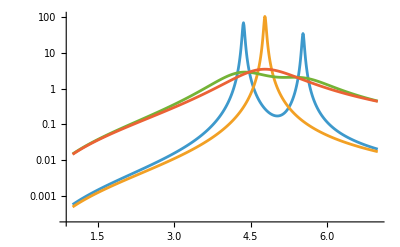

```mathematica
ListLinePlot[{qextAg0,qextAg1,qextAg0SC,qextAg1SC},PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
qextAg0SC=Table[{w,CextSC[1.5,1.5,1,1,w,omegaPAg,1,fjAg,omegaAg,gammaAg,hvFAg][[1]]},{w,1,7,0.01}];
qextAg1SC=Table[{w,CextSC[1.5,1.5,1.5,1,w,omegaPAg,1,fjAg,omegaAg,gammaAg,hvFAg][[1]]},{w,1,7,0.01}];
```

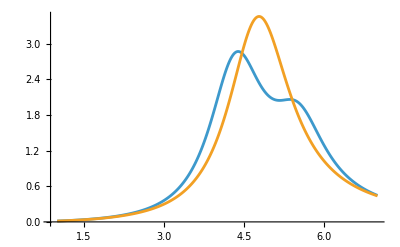

```mathematica
ListLinePlot[{qextAg0SC,qextAg1SC},PlotRange->All]
```

### 5 lorentzianas

```mathematica
omegasAu=Range[1,7,0.01];
AR={1,1.5,2,2.5,3,3.5,4,4.5,5,7,9};
```

```mathematica
qextAuSCListPlot6=Table[{w,CextSC[#,#,1,1,w,omegaPAu,6,fjAu,omegaAu,gammaAu,hvFAu][[1]]},{w,1,7,0.01}]&/@AR;
qextAuSCPlot06=Table[CextSC[#,#,1,1,w,omegaPAu,6,fjAu,omegaAu,gammaAu,hvFAu][[1]],{w,1,7,0.01}]&/@AR;
qextAuSCPlot6=Interpolation[Transpose[{omegasAu,qextAuSCPlot06[[#]]}]]&/@{1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
ResRojoAu06=GoldenSearchMax[qextAuSCPlot6[[#]],1.8,2.5] &/@{1,2,3,4,5,6,7,8,9};
ResAzulAu06=GoldenSearchMax[qextAuSCPlot6[[#]],4,5.6] &/@{1,2,3,4,5,6,7,8,9};
ResRojoAu16=GoldenSearchMax[qextAuSCPlot6[[10]],1.45,2.2] &/@{10,11};
ResAzulAu16=GoldenSearchMax[qextAuSCPlot6[[#]],3.8,4.9] &/@{10,11};
ResRojoAu6=Join[ResRojoAu06,ResRojoAu16];
ResAzulAu6=Join[ResAzulAu06,ResAzulAu16];
```

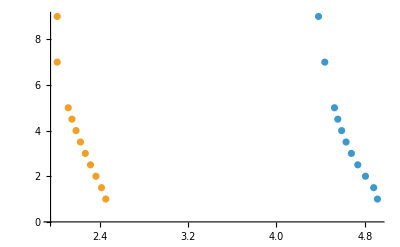

```mathematica
ListPlot[{Transpose[{ResAzulAu6,AR}],Transpose[{ResRojoAu6,AR}]}]
```

```mathematica
qextAgSCListPlot6=Table[{w,CextSC[#,#,1,1,w,omegaPAg,6,fjAg,omegaAg,gammaAg,hvFAg][[1]]},{w,1,7,0.01}]&/@AR;
qextAgSCPlot06=Table[CextSC[#,#,1,1,w,omegaPAg,6,fjAg,omegaAg,gammaAg,hvFAg][[1]],{w,1,7,0.01}]&/@AR;
qextAgSCPlot6=Interpolation[Transpose[{omegasAu,qextAgSCPlot06[[#]]}]]&/@{1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
ResRojoAg06=GoldenSearchMax[qextAgSCPlot6[[#]],2.2,4] &/@{1,2,3,4,5,6,7,8,9};
ResAzulAg06=GoldenSearchMax[qextAgSCPlot6[[#]],4.6,5.6] &/@{1,2,3,4,5,6,7,8,9};
ResRojoAg16=GoldenSearchMax[qextAgSCPlot6[[#]],2,2.8] &/@{10,11};
ResAzulAg16=GoldenSearchMax[qextAgSCPlot6[[#]],4.5,5.1] &/@{10,11};
ResRojoAg6=Join[ResRojoAg06,ResRojoAg16];
ResAzulAg6=Join[ResAzulAg06,ResAzulAg16];
```

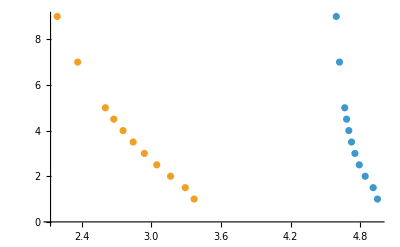

```mathematica
ListPlot[{Transpose[{ResAzulAg6,AR}],Transpose[{ResRojoAg6,AR}]}]
```

### 4 lorentzianas

```mathematica
omegasAu=Range[1,7,0.01];
AR={1,1.5,2,2.5,3,3.5,4,4.5,5,7,9};
```

```mathematica
qextAuSCListPlot5=Table[{w,CextSC[#,#,1,1,w,omegaPAu,5,fjAu,omegaAu,gammaAu,hvFAu][[1]]},{w,1,7,0.01}]&/@AR;
qextAuSCPlot05=Table[CextSC[#,#,1,1,w,omegaPAu,5,fjAu,omegaAu,gammaAu,hvFAu][[1]],{w,1,7,0.01}]&/@AR;
qextAuSCPlot5=Interpolation[Transpose[{omegasAu,qextAuSCPlot05[[#]]}]]&/@{1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
ResRojoAu05=GoldenSearchMax[qextAuSCPlot5[[#]],2,2.6] &/@{1,2,3,4,5,6,7,8,9};
ResAzulAu05=GoldenSearchMax[qextAuSCPlot5[[#]],4.4,5.6] &/@{1,2,3,4,5,6,7,8,9};
ResRojoAu15=GoldenSearchMax[qextAuSCPlot5[[10]],1.45,2.2] &/@{10,11};
ResAzulAu15=GoldenSearchMax[qextAuSCPlot5[[#]],3.8,4.9] &/@{10,11};
ResRojoAu5=Join[ResRojoAu05,ResRojoAu15];
ResAzulAu5=Join[ResAzulAu05,ResAzulAu15];
```

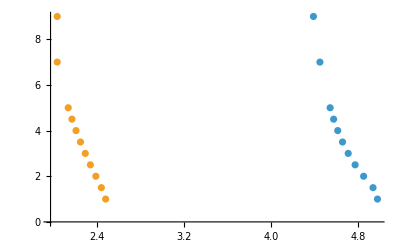

```mathematica
ListPlot[{Transpose[{ResAzulAu5,AR}],Transpose[{ResRojoAu5,AR}]}]
```

```mathematica
qextAgSCListPlot5=Table[{w,CextSC[#,#,1,1,w,omegaPAg,5,fjAg,omegaAg,gammaAg,hvFAg][[1]]},{w,1,7,0.01}]&/@AR;
qextAgSCPlot05=Table[CextSC[#,#,1,1,w,omegaPAg,5,fjAg,omegaAg,gammaAg,hvFAg][[1]],{w,1,7,0.01}]&/@AR;
qextAgSCPlot5=Interpolation[Transpose[{omegasAu,qextAgSCPlot05[[#]]}]]&/@{1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
ResRojoAg05=GoldenSearchMax[qextAgSCPlot5[[#]],2.4,4] &/@{1,2,3,4,5,6,7,8,9};
ResAzulAg05=GoldenSearchMax[qextAgSCPlot5[[#]],4.6,5.6] &/@{1,2,3,4,5,6,7,8,9};
ResRojoAg15=GoldenSearchMax[qextAgSCPlot5[[10]],2,2.8] &/@{10,11};
ResAzulAg15=GoldenSearchMax[qextAgSCPlot5[[#]],4.5,5.1] &/@{10,11};
ResRojoAg5=Join[ResRojoAg05,ResRojoAg15];
ResAzulAg5=Join[ResAzulAg05,ResAzulAg15];
```

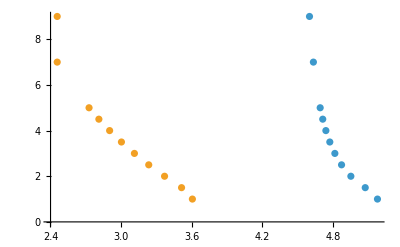

```mathematica
ListPlot[{Transpose[{ResAzulAg5,AR}],Transpose[{ResRojoAg5,AR}]}]
```

### 3 lorentzianas

```mathematica
omegasAu=Range[1,7,0.01];
AR={1,1.5,2,2.5,3,3.5,4,4.5,5,7,9};
```

```mathematica
qextAuSCListPlot4=Table[{w,CextSC[#,#,1,1,w,omegaPAu,4,fjAu,omegaAu,gammaAu,hvFAu][[1]]},{w,1,7,0.01}]&/@AR;
qextAuSCPlot04=Table[CextSC[#,#,1,1,w,omegaPAu,4,fjAu,omegaAu,gammaAu,hvFAu][[1]],{w,1,7,0.01}]&/@AR;
qextAuSCPlot4=Interpolation[Transpose[{omegasAu,qextAuSCPlot04[[#]]}]]&/@{1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
ResRojoAu04=GoldenSearchMax[qextAuSCPlot4[[#]],2.2,3] &/@{1,2,3,4,5,6,7,8,9};
ResAzulAu04=GoldenSearchMax[qextAuSCPlot4[[#]],4.3,5.3] &/@{1,2,3,4,5,6,7,8,9};
ResRojoAu14=GoldenSearchMax[qextAuSCPlot4[[#]],1.5,2.5] &/@{10,11};
ResAzulAu14=GoldenSearchMax[qextAuSCPlot4[[#]],3.8,4.9] &/@{10,11};
ResRojoAu4=Join[ResRojoAu04,ResRojoAu14];
ResAzulAu4=Join[ResAzulAu04,ResAzulAu14];
```

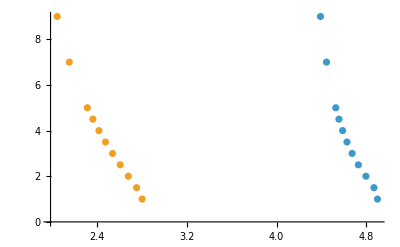

```mathematica
ListPlot[{Transpose[{ResAzulAu4,AR}],Transpose[{ResRojoAu4,AR}]}]
```

```mathematica
qextAgSCListPlot4=Table[{w,CextSC[#,#,1,1,w,omegaPAg,4,fjAg,omegaAg,gammaAg,hvFAg][[1]]},{w,1,7,0.01}]&/@AR;
qextAgSCPlot04=Table[CextSC[#,#,1,1,w,omegaPAg,4,fjAg,omegaAg,gammaAg,hvFAg][[1]],{w,1,7,0.01}]&/@AR;
qextAgSCPlot4=Interpolation[Transpose[{omegasAu,qextAgSCPlot04[[#]]}]]&/@{1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
ResRojoAg04=GoldenSearchMax[qextAgSCPlot4[[#]],2.5,4] &/@{1,2,3,4,5,6,7,8,9};
ResAzulAg04=GoldenSearchMax[qextAgSCPlot4[[#]],4.6,5.9] &/@{1,2,3,4,5,6,7,8,9};
ResRojoAg14=GoldenSearchMax[qextAgSCPlot4[[#]],1.9,3.5] &/@{10,11};
ResAzulAg14=GoldenSearchMax[qextAgSCPlot4[[#]],4.3,5.1] &/@{10,11};
ResRojoAg4=Join[ResRojoAg04,ResRojoAg14];
ResAzulAg4=Join[ResAzulAg04,ResAzulAg14];
```

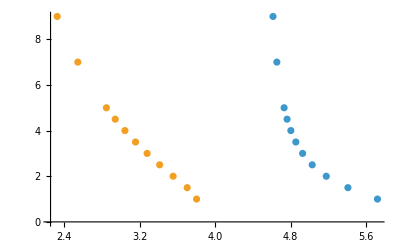

```mathematica
ListPlot[{Transpose[{ResAzulAg4,AR}],Transpose[{ResRojoAg4,AR}]}]
```

### 2 lorentzianas

```mathematica
omegasAu=Range[1,7,0.01];
AR={1,1.5,2,2.5,3,3.5,4,4.5,5,7,9};
```

```mathematica
qextAuSCListPlot3=Table[{w,CextSC[#,#,1,1,w,omegaPAu,3,fjAu,omegaAu,gammaAu,hvFAu][[1]]},{w,1,7,0.01}]&/@AR;
qextAuSCPlot03=Table[CextSC[#,#,1,1,w,omegaPAu,3,fjAu,omegaAu,gammaAu,hvFAu][[1]],{w,1,7,0.01}]&/@AR;
qextAuSCPlot3=Interpolation[Transpose[{omegasAu,qextAuSCPlot03[[#]]}]]&/@{1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
ResRojoAu03=GoldenSearchMax[qextAuSCPlot3[[#]],2.1,3.1] &/@{1,2,3,4,5,6,7,8,9};
ResAzulAu03=GoldenSearchMax[qextAuSCPlot3[[#]],4.5,6.6] &/@{1,2,3,4,5,6,7,8,9};
ResRojoAu13=GoldenSearchMax[qextAuSCPlot3[[#]],1.5,2.5] &/@{10,11};
ResAzulAu13=GoldenSearchMax[qextAuSCPlot3[[#]],3.8,4.9] &/@{10,11};
ResRojoAu3=Join[ResRojoAu03,ResRojoAu13];
ResAzulAu3=Join[ResAzulAu03,ResAzulAu13];
```

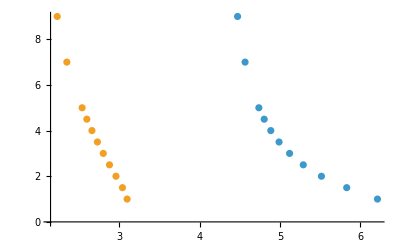

```mathematica
ListPlot[{Transpose[{ResAzulAu3,AR}],Transpose[{ResRojoAu3,AR}]}]
```

```mathematica
qextAgSCListPlot3=Table[{w,CextSC[#,#,1,1,w,omegaPAg,3,fjAg,omegaAg,gammaAg,hvFAg][[1]]},{w,1,7,0.01}]&/@AR;
qextAgSCPlot03=Table[CextSC[#,#,1,1,w,omegaPAg,3,fjAg,omegaAg,gammaAg,hvFAg][[1]],{w,1,7,0.01}]&/@AR;
qextAgSCPlot3=Interpolation[Transpose[{omegasAu,qextAgSCPlot03[[#]]}]]&/@{1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
ListLinePlot[qextAgSCListPlot3[[10]],PlotRange->All]
```

```mathematica
ResRojoAg03=GoldenSearchMax[qextAgSCPlot3[[#]],2.5,4] &/@{1,2,3,4,5,6,7,8,9};
ResAzulAg03=GoldenSearchMax[qextAgSCPlot3[[#]],4.6,5.9] &/@{1,2,3,4,5,6,7,8,9};
ResRojoAg13=GoldenSearchMax[qextAgSCPlot3[[#]],1.9,3.5] &/@{10,11};
ResAzulAg13=GoldenSearchMax[qextAgSCPlot3[[#]],4.3,5.1] &/@{10,11};
ResRojoAg3=Join[ResRojoAg03,ResRojoAg13];
ResAzulAg3=Join[ResAzulAg03,ResAzulAg13];
```

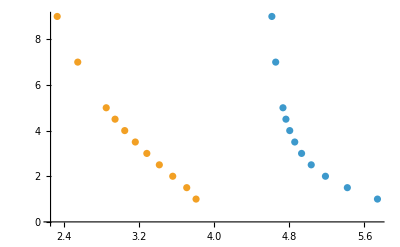

```mathematica
ListPlot[{Transpose[{ResAzulAg3,AR}],Transpose[{ResRojoAg3,AR}]}]
```

```mathematica
h vlight/7
```

177.243

### 1 lorentziana

```mathematica
omegasAu=Range[1,7,0.01];
AR={1,1.5,2,2.5,3,3.5,4,4.5,5,7,9};
```

```mathematica
qextAuSCListPlot2=Table[{w,CextSC[#,#,1,1,w,omegaPAu,2,fjAu,omegaAu,gammaAu,hvFAu][[1]]},{w,1,7,0.01}]&/@AR;
qextAuSCPlot02=Table[CextSC[#,#,1,1,w,omegaPAu,2,fjAu,omegaAu,gammaAu,hvFAu][[1]],{w,1,7,0.01}]&/@AR;
qextAuSCPlot2=Interpolation[Transpose[{omegasAu,qextAuSCPlot02[[#]]}]]&/@{1,2,3,4,5,6,7,8,9,10,11};
```

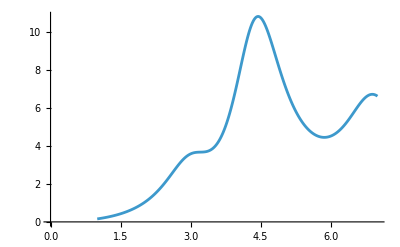

```mathematica
ListLinePlot[qextAuSCListPlot2[[4]]]
```

```mathematica
ResRojoAu02=GoldenSearchMax[qextAuSCPlot2[[#]],2.4,3.4] &/@{1,2};
ResAzulAu02=GoldenSearchMax[qextAuSCPlot2[[#]],4.6,5.3] &/@{1,2};
ResRojoAu12=GoldenSearchMax[qextAuSCPlot2[[#]],3.16,3.18] &/@{3,4,5};
ResAzulAu12=GoldenSearchMax[qextAuSCPlot2[[#]],4.5,6.6] &/@{1,2,3,4,5,6,7,8,9};
ResRojoAu12=GoldenSearchMax[qextAuSCPlot2[[#]],1.5,2.5] &/@{10,11};
ResAzulAu12=GoldenSearchMax[qextAuSCPlot2[[#]],3.8,4.9] &/@{10,11};
ResRojoAu2=Join[ResRojoAu02,ResRojoAu12];
ResAzulAu2=Join[ResAzulAu02,ResAzulAu12];
```

```mathematica
ListPlot[{Transpose[{ResAzulAu3,AR}],Transpose[{ResRojoAu3,AR}]}]
```

-Graphics-

```mathematica
qextAgSCListPlot3=Table[{w,CextSC[#,#,1,1,w,omegaPAg,3,fjAg,omegaAg,gammaAg,hvFAg][[1]]},{w,1,7,0.01}]&/@AR;
qextAgSCPlot03=Table[CextSC[#,#,1,1,w,omegaPAg,3,fjAg,omegaAg,gammaAg,hvFAg][[1]],{w,1,7,0.01}]&/@AR;
qextAgSCPlot3=Interpolation[Transpose[{omegasAu,qextAgSCPlot03[[#]]}]]&/@{1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
ListLinePlot[qextAgSCListPlot3[[10]],PlotRange->All]
```

```mathematica
ResRojoAg03=GoldenSearchMax[qextAgSCPlot3[[#]],2.5,4] &/@{1,2,3,4,5,6,7,8,9};
ResAzulAg03=GoldenSearchMax[qextAgSCPlot3[[#]],4.6,5.9] &/@{1,2,3,4,5,6,7,8,9};
ResRojoAg13=GoldenSearchMax[qextAgSCPlot3[[#]],1.9,3.5] &/@{10,11};
ResAzulAg13=GoldenSearchMax[qextAgSCPlot3[[#]],4.3,5.1] &/@{10,11};
ResRojoAg3=Join[ResRojoAg03,ResRojoAg13];
ResAzulAg3=Join[ResAzulAg03,ResAzulAg13];
```

```mathematica
ListPlot[{Transpose[{ResAzulAg3,AR}],Transpose[{ResRojoAg3,AR}]}]
```

-Graphics-

### Solo Drude

```mathematica
omegasAu=Range[1,7,0.01];
AR={1,1.5,2,2.5,3,3.5,4,4.5,5,7,9};
```

```mathematica
qextAuSCListPlot1=Table[{w,CextSC[#,#,1,1,w,omegaPAu,1,fjAu,omegaAu,gammaAu,hvFAu][[1]]},{w,1,7,0.01}]&/@AR;
qextAuSCPlot01=Table[CextSC[#,#,1,1,w,omegaPAu,1,fjAu,omegaAu,gammaAu,hvFAu][[1]],{w,1,7,0.01}]&/@AR;
qextAuSCPlot1=Interpolation[Transpose[{omegasAu,qextAuSCPlot01[[#]]}]]&/@{1,2,3,4,5,6,7,8,9,10,11};
```

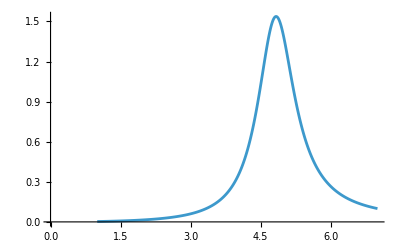

```mathematica
ListLinePlot[qextAuSCListPlot1[[1]]]
```

```mathematica
ResAu01=GoldenSearchMax[qextAuSCPlot1[[#]],1.4,5] &/@{1,2,3,4,5,6,7,8,9,10,11};
```

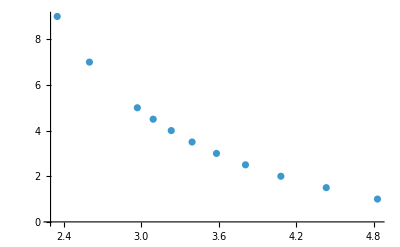

```mathematica
ListPlot[Transpose[{ResAu01,AR}]]
```

```mathematica
qextAgSCListPlot3=Table[{w,CextSC[#,#,1,1,w,omegaPAg,3,fjAg,omegaAg,gammaAg,hvFAg][[1]]},{w,1,7,0.01}]&/@AR;
qextAgSCPlot03=Table[CextSC[#,#,1,1,w,omegaPAg,3,fjAg,omegaAg,gammaAg,hvFAg][[1]],{w,1,7,0.01}]&/@AR;
qextAgSCPlot3=Interpolation[Transpose[{omegasAu,qextAgSCPlot03[[#]]}]]&/@{1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
ListLinePlot[qextAgSCListPlot3[[10]],PlotRange->All]
```

```mathematica
ResRojoAg03=GoldenSearchMax[qextAgSCPlot3[[#]],2.5,4] &/@{1,2,3,4,5,6,7,8,9};
ResAzulAg03=GoldenSearchMax[qextAgSCPlot3[[#]],4.6,5.9] &/@{1,2,3,4,5,6,7,8,9};
ResRojoAg13=GoldenSearchMax[qextAgSCPlot3[[#]],1.9,3.5] &/@{10,11};
ResAzulAg13=GoldenSearchMax[qextAgSCPlot3[[#]],4.3,5.1] &/@{10,11};
ResRojoAg3=Join[ResRojoAg03,ResRojoAg13];
ResAzulAg3=Join[ResAzulAg03,ResAzulAg13];
```

```mathematica
ListPlot[{Transpose[{ResAzulAg3,AR}],Transpose[{ResRojoAg3,AR}]}]
```

-Graphics-